(-1+λ^4)/((1+(-2+4 ζ^2) λ^2+λ^4)^(3/2))==0

{{λ→-1},{λ→-ⅈ},{λ→ⅈ},{λ→1}}

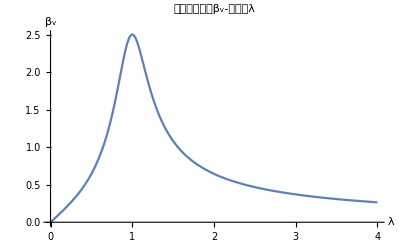

```mathematica
Subscript[β, v][λ_]:=λ/(√((1-λ^2)^2+(2 ζ λ)^2));
eq=Simplify[D[Subscript[β, v][λ],λ]==0]
Solve[eq,λ]
Subscript[pic, 1]=Plot[Subscript[β, v][λ]/.ζ->0.2,{λ,0,4}];
Show[Subscript[pic, 1],AxesLabel->{HoldForm[λ],HoldForm[Subscript[β, v]]},PlotLabel->HoldForm[Subscript[速度放大因子β, v]-频率比λ],LabelStyle->{GrayLevel[0]}]
```

(λ (-1+2 ζ^2+λ^2))/((1+(-2+4 ζ^2) λ^2+λ^4)^(3/2))==0

{{λ→0},{λ→-√(1-2 ζ^2)},{λ→√(1-2 ζ^2)}}

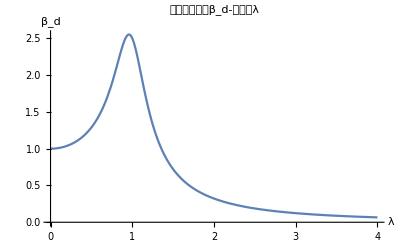

```mathematica
Subscript[β, d][λ_]:=1/(√((1-λ^2)^2+(2 ζ λ)^2));
eq=Simplify[D[Subscript[β, d][λ],λ]==0]
Solve[eq,λ]
Subscript[pic, 2]=Plot[Subscript[β, d][λ]/.ζ->0.2,{λ,0,4}];
Show[Subscript[pic, 2],AxesLabel->{HoldForm[λ],HoldForm[Subscript[β, d]]},PlotLabel->HoldForm[Subscript[位移放大因子β, d]-频率比λ],LabelStyle->{GrayLevel[0]}]
```

(λ+(-1+2 ζ^2) λ^3)/((1+(-2+4 ζ^2) λ^2+λ^4)^(3/2))==0

{{λ→0},{λ→-1/(√(1-2 ζ^2))},{λ→1/(√(1-2 ζ^2))}}

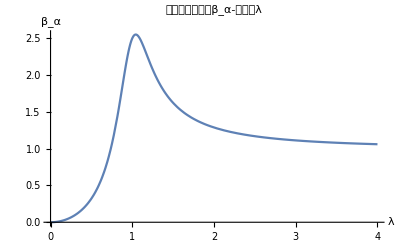

```mathematica
Subscript[β, α][λ_]:=λ^2/(√((1-λ^2)^2+(2 ζ λ)^2));
eq=Simplify[D[Subscript[β, α][λ],λ]==0]
Solve[eq,λ]
Subscript[pic, 3]=Plot[Subscript[β, α][λ]/.ζ->0.2,{λ,0,4}];
Show[Subscript[pic, 3],AxesLabel->{HoldForm[λ],HoldForm[Subscript[β, α]]},PlotLabel->HoldForm[Subscript[加速度放大因子β, α]-频率比λ],LabelStyle->{GrayLevel[0]}]
```